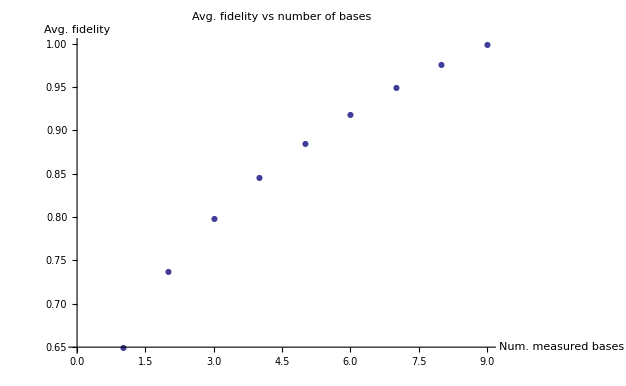

```mathematica
bases ={9, 8, 7, 6, 5, 4, 3,2,1};
fids = {0.999, 0.976,0.949,0.918, 0.885, 0.846, 0.798,0.737, 0.650};
times = {518.870,501.368, 483.277,466.364, 448.547, 428.746,412.304,394.760,357.285};

ListPlot[Transpose[{bases,fids}],PlotMarkers->{Automatic,8}, PlotLabel->"Avg. fidelity vs number of bases", AxesLabel->{"Num. measured bases", "Avg. fidelity"}]
```

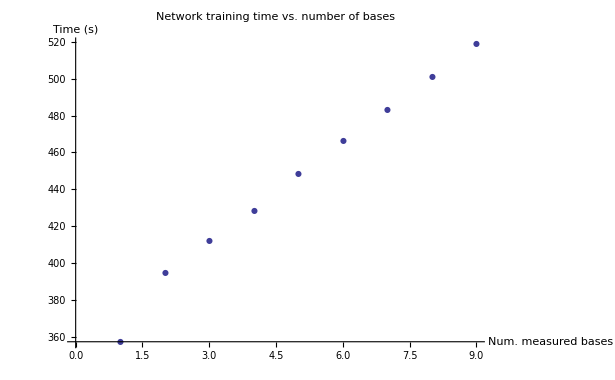

```mathematica
ListPlot[Transpose[{bases,times}],PlotMarkers->{Automatic,8}, PlotLabel->"Network training time vs. number of bases", AxesLabel->{"Num. measured bases", "Time (s)"}]
```

```mathematica
ListPlot[Transpose[{bases,times}],PlotMarkers->{Automatic,8}, PlotLabel->"Network training time vs. number of bases"]
```